```mathematica
(*spin_rotation_angle_20250115: attempt to add garnet and contaminant magnetizations before determining Tc*)(*spin_rotation_angle_20250109: total magnetization reverted to conventional signs - below Tc, M > 0; adjusted contaminants accordingly; study various field coefficient dependence*)
(*spin_rotation_angle_20241030: Molecular field calculation added to notebook*)
(*spin_rotation_angle_20241025_2: Total magnetization negated to match direction taken as positive*)
(*spin_rotation_angle_20241025: added perovskite and hematite contributions*)
(*spin_rotation_angle_20240920: sample geometry matches 2024 arXiv preprint*)
```

```mathematica
(*Magnetization from molecular field theory*)
Clear[dT,Tm,NA,muB,rho,A,kB,h,naa,nad,ndd,nac,ncc,ndd,Jc,Sc,Lc,Ja,Sa,La,Jd,Sd,Ld,gamma,Lcpp,Jcpp,d,gc,gcs,ga,gd,gcpp,muc0,mua0,mud0,xc,xa,xd,bjc,bja,bjd,rtr,n,muct,muat,mudt,must,i,tc,muctc,muatc,mudtc,sctc,sxtc,mutp,musti,imust,mustp,imustp,Treq,lTreq,Mreq,mutp];

(*input*)
(*Temperature parameters*)
dT=1.;   (*increment, K*)
Tm=400;  (*maximum, K*)

(*physical constants*)
NA=6.02 10^23;(*Avogadro*)
muB=9.274 10^-21;(*Bohr magneton,erg/G*)
kB=1.381 10^-16 ;(*Boltzmann, erg/K*)

(*field coefficients in mol/cc*)
naa=-65.0;  (*octahedral-octahedral[Dionne71]*)
nad=97.0;     (*octahedral-tetrahedral[Dionne71]*)
ndd=-30.4;(*tetrahedral-tetrahedral[Dionne71]*)

nac=-4.2 ;(*octahedral-dodecahedral[Dionne79, Dionne09]*)
ncc=0.;   (*dodecahedral-dodecahedral[Dionne79, Dionne09]*)
ncd=6.5;  (*dodecahedral-tetrahedral[Dionne79, Dionne09]*)

(*
naa=-51;(*new best fit to HFIR*)
nad=82.3;(*new best fit to HFIR*)
ndd=-33;(*new best fit to HFIR*)

nac=-3;(*new best fit to HFIR*)
ncc=0.;   (*new best fit to HFIR*)
ncd=5;  (*new best fit to HFIR*)
*)

(*angular momenta in hbar[Dionne09]*)
gamma=0.32; (*quenching factor*)
gamma=1;
(*gamma=0.25;(*quenching factor to yield Tc = 250 K, empirical*)*)
Sc=3;(*Tb spin*)
Lc=gamma 3;(*Tb orbit*)
Jc=Lc+Sc;(*Tb total*)
Jc=4.6;
Sa=5/2;(*Fe spin*)

Sd=5/2;(*Fe spin*)


(*calculations*)
(*g-factors*)
(*gc=(Lc+2 Sc)/(Lc+Sc)*)
gc=1+(Jc (Jc+1)+Sc (Sc+1)-Lc (Lc+1))/(2 Jc (Jc+1)); (*rare earth*)
gcs=1+(Sc (Sc+1)-Lc (Lc+1))/(Jc (Jc+1));                            (*rare earth spin*)
ga=2.;                                                                                                                    (*Fe,all spin*)
gd=2.;                                                                                                                    (*Fe,all spin*)

(*initial magnetization,T=0*)
muc0=3. gc Jc muB NA;
mua0=2. ga Sa muB NA;
mud0=3. gd Sd muB NA;

(*molecular fields*)
xc=(Jc gc muB)/(kB dT (n+1)) (ncc muc[n]+nac mua[n]+ncd mud[n]);
xa=(Sa ga muB)/(kB dT (n+1)) (naa mua[n]+nac muc[n]+nad mud[n]);
xd=(Sd gd muB)/(kB dT (n+1)) (ndd mud[n]+ncd muc[n]+nad mua[n]);

(*Brillouin functions*)
bjc=((2 Jc+1)/(2 Jc)) Coth[(2 Jc+1) xc/(2 Jc)]-(1/(2 Jc)) Coth[xc/(2 Jc)];
bja=((2 Sa+1)/(2 Sa)) Coth[(2 Sa+1) xa/(2 Sa)]-(1/(2 Sa)) Coth[xa/(2 Sa)];
bjd=((2 Sd+1)/(2 Sd)) Coth[(2 Sd+1) xd/(2 Sd)]-(1/(2 Sd)) Coth[xd/(2 Sd)];

(*solve recurrence equations for moments at successive T*)rtr=RecurrenceTable[{muc[n+1]==muc0 bjc,mua[n+1]==mua0 bja,mud[n+1]==mud0 bjd,muc[0]==muc0,mua[0]==mua0,mud[0]==mud0},{muc,mua,mud},{n,0,Tm}];

(*moment vs.T lists*)
muct=Table[{i dT,rtr[[i+1,1]]/(muB NA)},{i,1,Tm}];
muat=Table[{i dT,rtr[[i+1,2]]/(muB NA)},{i,1,Tm}];
mudt=Table[{i dT,-rtr[[i+1,3]]/(muB NA)},{i,1,Tm}];
must=Table[{i dT,Abs[rtr[[i+1,1]]+rtr[[i+1,2]]-rtr[[i+1,3]]]/(muB NA)},{i,1,Tm}];
imuct=Interpolation[muct];
imuat=Interpolation[muat];
imudt=Interpolation[mudt];

(*find Tc*)
tc=Position[must,Min[must[[All,2]]]][[1,1]];
(*interpolation*)musti=Table[{i dT,(rtr[[i+1,1]]+rtr[[i+1,2]]-rtr[[i+1,3]])/(muB NA)},{i,1,Tm}];
imust=Interpolation[musti];

tc=FindRoot[imust[T]==0.,{T,100.}][[1,2]];(*revised TC: get moment as function of T, then find root*)

(*contribution of rare earth at Tc*)
muctc=imuct[tc];
muatc=imuat[tc];
mudtc=imudt[tc];
sctc=(gcs/gc) muctc;
sxtc=sctc+muatc+mudtc;


(*total moment and magnetization*)
Clear[NA,u,muBSI,mTb,mFe,mO,m03f1,v03f1,m03f1r,v03f1r,mTbIG,ng03f1,MT03f1,M03f1,pur,perovMomenti,iperovMoment,hemMomentt,hemMomentm,hemMomenti,ihemMoment,perovPct,hemPct,mPerov,mHemat,np03f1,nh03f1,tct,Ttreq,lTtreq,s0,BT,d,TC];
(*data*)
NA=6.022*10^23;
u=1.66 10^-27;(*amu, kg*)
muBSI = (1 10^-3)muB;(*Bohr Magneton, J/T*)
mTb = 158.93;(*Tb mass, u*)
mFe = 55.854;(*Fe mass, u*)
mO=15.999;(*O mass, u*)
m03f1=8.598 10^-3;(*sample mass, kg*)
m03f1r=7.973 10^-3;(*revised sample mass, kg*)
v03f1 = 2.118 10^-6;(*sample volume, m^3*)
v03f1r = 2.098 10^-6;(*revised sample volume, m^3*)
pur=0.887;(*purity (% of garnet phase)*)
s0=0.039;(*zero-T perovskite moment [Treves1965],uB/molecule*)
BT=0.95;(*pure S=5/2 ferromagnet T-dependence, approx.[Dionne2009]*)
d=0.32;(*Fe-Tb interaction parameter [Treves1965]]*)
TC = 650.;(*perovskite Curie T [Treves1965], K]*)
(*calculations*)
(*perovMoment ={0.075,.072,.070,.067}; (*uB/molecule for perovskite [Park2008], this was ZFC at 300Oe applied field so may not be valid*)*)
(*perovMoment ={0.039,.039,.039,.039}; (*s0 (interpretation 1 of old data) [Treves1965]*)*)
perovMomenti=Table[{i dT,(-s0 BT (1.+d TC/i))},{i,1,Tm}];(*perovskite moment, uB/molecule; convention is negative*)
iperovMoment=Interpolation[perovMomenti];(*interpolated perovskite moment*)
hemMomentt={1.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.,210.,220.,230.,240.,250.,260.,270.,280.,290.,300.};(*hematite moment T data [Andre-Filho2014]]*)
hemMomentm=-(159.69/NA*1.078*10^20){0.019,0.019,0.019,0.019,0.019,0.019,0.0191,0.0192,0.0193,0.0194,0.0195,0.0196,0.0197,0.0198,0.0199,0.02,0.0201,0.0202,0.0205,0.021,0.0215,0.022,0.023,0.025,0.03,0.04,0.06,0.09,.11,.12,.123};(*hematite moment data [Andre-Filho2014],from emu/g to uB/molecule, convention is negative*)
hemMomenti=Table[{hemMomentt[[i]],hemMomentm[[i]]},{i,1,31}];(*hematite moment data [Andre-Filho2014]]*)
ihemMoment=Interpolation[hemMomenti];(*interpolated hematite moment*)
perovPct = .086;
hemPct = .027;
mTbIG = 3.0 mTb+5.0 mFe+12.0 mO;(*TbIG mass, u*)
mPerov = mTb + mFe + 3.0 mO;(*perovskite mass, u*)
mHemat = 2.0 mFe + 3.0 mO;(*hematite mass, u*)
ng03f1=pur m03f1r /(u mTbIG);(*molecules of garnet*)
np03f1 = perovPct m03f1r/(u mPerov);(*molecules of perovskite*)
nh03f1 = hemPct m03f1r /(u mHemat); (*molecules of hematite*)
tct=FindRoot[(muBSI ng03f1 imust[T]+muBSI  np03f1 iperovMoment[T]+muBSI  nh03f1 ihemMoment[T])==0.,{T,100.}][[1,2]];(*total TC: compute total moment as function of T, then find root*)

(*spin rotation angle*)
Clear[zmin,zmax,mu0,gn,mn,ln,h,ae,zd,Bza,z,BzaPlt,phi,Bzsg];
zmin=-.508/2;
zmax=.508/2;
mu0=(4. Pi) 10^-7;  (*perm.free space,N/(A^2)*)
gn = 1.832 10^8;(*neutron gyromagnetic ratio, 1/(sT)*)
mn=1.675 10^-27;(*neutron mass, kg*)
ln=2.5 10^-10;(*neutron wavelength, m*)
h = 6.626 10^-34;(*Planck constant, Js*)
ae=9.5 10^-3; (*sample radius, m*)
zd=7.4 10^-3;   (*sample z-size,m*)
```

```mathematica
(*Generate angle interpolating function*)

(*matching the compensation points*)
tcTempSweep=250.03;
tcShift=Round[tcTempSweep]-Round[tct];
tcShift=tct-tcTempSweep;
(*shiftedmusti=musti[[240-tcShift;;260-tcShift]]/. {x_,y_}:>{x+tcShift,y};*)
(*shiftedimust=imust[[240-tcShift;;260-tcShift]]/. {x_,y_}:>{x+tcShift,y};*)

low=240;
high=261;

hemMomentTable=Table[{x,ihemMoment[x]},{x,low,high+tcShift,1}];
perovMomentTable=Table[{x,iperovMoment[x]},{x,low,high+tcShift,1}];
garnetMomentTable=Table[{x,imust[x]},{x,low,high+tcShift,1}];

(*Table of total magnetizations, A/m*)
totalMagTable=MapThread[{#1[[1]]-tcShift,(muBSI ng03f1 #1[[2]]+muBSI  np03f1#2[[2]]+muBSI  nh03f1#3[[2]])/v03f1r }&,{garnetMomentTable,perovMomentTable,hemMomentTable}];

(*Scaling factor function; quadratic w/ fixed mean*)
a=-6.9*10^(-5); (*actual scaling factor fit*)
b=0.682;

(*a=-2*10^(-5);(*better scaling factor fit*)
b=0.65;*)

f[x_]:=a(x-tcTempSweep)^2+b;
scalingTable=Table[{x,f[x]},{x,240,261,1}];

(*scaling by remanent scale factor and demagnetization, 0.344*)
scaledMagStatic=MapThread[{#1[[1]],#1[[2]]*0.68*0.344}&,{totalMagTable}];
scaledMag=MapThread[{#1[[1]],#1[[2]]*#2[[2]]*0.344}&,{totalMagTable,scalingTable}];

(*Getting table of mag fields from 200 to 300*)
BzaTable=({#[[1]],-(mu0#[[2]]/2)((z-zd/2)/((ae^2+(z-zd/2)^2)^(1/2))-(z+zd/2)/((ae^2+(z+zd/2)^2)^(1/2)))}&)/@scaledMag;

(*table of rotation angles from 200 to 300*)
phiTable=({#[[1]],(gn mn ln/h)Integrate[#[[2]],{z,zmin,zmax}]}&)/@BzaTable;
```

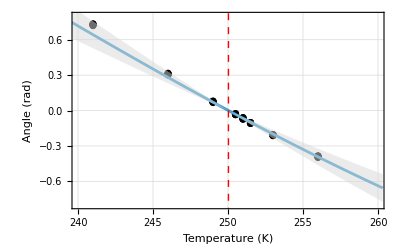

```mathematica
(*Import CSV*)
data=Import["/Users/beckethill/Documents/Research/NSR/2023_Mono_Temp_Corrected.csv"];

Needs["ErrorBarPlots`"];
(*Extract columns*)
temp=N[data[[1;;49,1]]];  
angle=N[data[[1;;49,2]]];  
temperror=N[data[[1;;49,3]]];  
angleerror=1*10^-8;


modelAngle=phiTable[[All,2]];
(*combining scaling factor, demag and coeff uncertainty*)
modelAngleError=Sqrt[(0.03)^2+(0.047)^2+(0.169)^2]*phiTable[[All,2]];
modelTemps=phiTable[[All,1]];
upper=modelAngle+modelAngleError;
lower=modelAngle-modelAngleError;


angleData=Table[{temp[[i]],angle[[i]]},{i,1,Length[temp]}];

angleDataPlot=ListPlot[angleData,PlotRange->{{240,260},{-0.8,0.8}},PlotStyle->Black,GridLines->Automatic,Frame->True,FrameTicksStyle->Directive[FontSize->12,Black],FrameLabel->{Style["Temperature (K)",Black,16],Style["Angle (rad)",Black,16]},Epilog->{Directive[Red,Dashed,Thick],Line[{{250.03,-1},{250.03,1}}]}];
angleModelPlot=ListLinePlot[phiTable];
shade=Graphics[{LightGray,Opacity[0.5],Polygon[Join[Transpose[{modelTemps,upper}],Reverse[Transpose[{modelTemps,lower}]]]]}];

anglePlots=Show[angleDataPlot,angleModelPlot,shade]
Export["/Users/beckethill/documents/research/NSR/Angle vs Temp.png",anglePlots];
```